```mathematica
(*
Hofstadter RG flow equation solver and plotting
for arXiv:2204.13116
even q version
*)
```

```mathematica
(*Packages for plotting*)
Get["SciDraw`"]
Get["CustomTicks`"]
```

```mathematica
(*parameters*)
p=1;
q=2;
dph=1; (*detuning parameter*)
V0=1;  (*on-site interactions*)
V1=0; (*on-site interactions*)
```

```mathematica
(*build the Hamiltonian*)

T=1;
H[k_,p_,q_]:=DiagonalMatrix[Table[-2T Cos[k[[2]]+2Pi p s/q],{s,0,q-1}]]+DiagonalMatrix[Table[-T Exp[-I k[[1]]],{s,0,q-2}],1]+DiagonalMatrix[{-T Exp[-I  k[[1]]]},1-q] +DiagonalMatrix[Table[-T Exp[I  k[[1]]],{s,0,q-2}],-1]+DiagonalMatrix[{-T Exp[I  k[[1]]]},q-1] //N
```

```mathematica
Clear[U]
```

```mathematica
(*build the Hamiltonian*)

T=1;
H[k_,p_,q_]:=DiagonalMatrix[Table[-2T Cos[k[[2]]+2Pi p s/q],{s,0,q-1}]]+DiagonalMatrix[Table[-T Exp[-I k[[1]]],{s,0,q-2}],1]+DiagonalMatrix[{-T Exp[-I  k[[1]]]},1-q] +DiagonalMatrix[Table[-T Exp[I  k[[1]]],{s,0,q-2}],-1]+DiagonalMatrix[{-T Exp[I  k[[1]]]},q-1] //N


(*build diagonalizing transformation u(k) with the sublattice and the band indices*)


Umat[k_,p_,q_]:=Module[{vals,vecs,Umatrix},{vals,vecs} = Eigensystem[H[k,p,q]];Umatrix = Inverse[Transpose[(Normalize/@vecs)[[Ordering[vals]]]]];DiagonalMatrix[Table[Exp[-I 0 Arg[Umatrix[[j,1]]]],{j,1,q}]].Umatrix]
U=ConstantArray[0,{q,3}];
U[[1,3]]=Umat[{0,Pi/q},p,q];
U[[1,2]]=Umat[{Pi/q,0},p,q];
U[[1,1]]=Umat[{0,-Pi/q},p,q];
(*U[[1,1]]=Table[U[[1,3]] [[Mod[m,q]+1,Mod[n-ModularInverse[p,q],q]+1]],{m,0,q-1},{n,0,q-1}];*)
For[l=1,l<q,l++,
For[v=-1,v<2,v++,
U[[Mod[l,q]+1,Mod[v,3,-1]+2]]=Table[U[[1,Mod[v,3,-1]+2]] [[Mod[m,q]+1,Mod[n+ModularInverse[p,q]*l,q]+1]],{m,0,q-1},{n,0,q-1}];
]
]
Clear[l,v]
```

```mathematica
(*define the momenta of the patches*)

P[q_,l_,v_]:={Mod[v+1,2]Pi/q,Mod[2l+v,2q]Pi/q}
```

```mathematica
(*function calculating the projected coupling constants with NN *)

CouplingConstant[p_,q_,band_,l_,u_,m_,v_,n_,w_]:=V0 Sum[U[[Mod[l+n,q]+1,Mod[u+w,3,-1]+2]][[band+1,sublattice+1]]U[[Mod[-n,q]+1,Mod[-w,3,-1]+2]][[band+1,sublattice+1]]Conjugate[U[[Mod[-m ,q]+1,Mod[-v,3,-1]+2]][[band+1,sublattice+1]]]Conjugate[U[[Mod[l+m,q]+1,Mod[u+v,3,-1]+2]][[band+1,sublattice+1]]],{sublattice,0,q-1}]+
V1 Sum[Cos[(P[q,-n,-w][[2]]-P[q,-m,-v][[2]])]U[[Mod[l+n,q]+1,Mod[u+w,3,-1]+2]][[band+1,sublattice+1]]U[[Mod[-n,q]+1,Mod[-w,3,-1]+2]][[band+1,sublattice+1]]Conjugate[U[[Mod[-m ,q]+1,Mod[-v,3,-1]+2]][[band+1,sublattice+1]]]Conjugate[U[[Mod[l+m,q]+1,Mod[u+v,3,-1]+2]][[band+1,sublattice+1]]],{sublattice,0,q-1}]+V1 Sum[Exp[I(P[q,-n,-w][[1]]-P[q,-m,-v][[1]])]U[[Mod[l+n,q]+1,Mod[u+w,3,-1]+2]][[band+1,sublattice+1]]U[[Mod[-n,q]+1,Mod[-w,3,-1]+2]][[band+1,Mod[sublattice+1,q]+1]]Conjugate[U[[Mod[-m ,q]+1,Mod[-v,3,-1]+2]][[band+1,Mod[sublattice+1,q]+1]]]Conjugate[U[[Mod[l+m,q]+1,Mod[u+v,3,-1]+2]][[band+1,sublattice+1]]],{sublattice,0,q-1}]/2+V1 Sum[Exp[-I(P[q,-n,-w][[1]]-P[q,-m,-v][[1]])]U[[Mod[l+n,q]+1,Mod[u+w,3,-1]+2]][[band+1,sublattice+1]]U[[Mod[-n,q]+1,Mod[-w,3,-1]+2]][[band+1,Mod[sublattice-1,q]+1]]Conjugate[U[[Mod[-m ,q]+1,Mod[-v,3,-1]+2]][[band+1,Mod[sublattice-1,q]+1]]]Conjugate[U[[Mod[l+m,q]+1,Mod[u+v,3,-1]+2]][[band+1,sublattice+1]]],{sublattice,0,q-1}]/2
```

```mathematica
(*functions*)

g1:=Function[{i,j},ToExpression["gI"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
g1p:=Function[{i,j},ToExpression["gIp"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
g2:=Function[{i,j},ToExpression["gII"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
g3:=Function[{i,j},ToExpression["gIII"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
g4:=Function[{i,j},ToExpression["gIV"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];

g1L1:=Function[{i,j},ToExpression["gIL1"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
g1pL1:=Function[{i,j},ToExpression["gIpL1"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
g2L1:=Function[{i,j},ToExpression["gIIL1"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
g3L1:=Function[{i,j},ToExpression["gIIIL1"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
g4L1:=Function[{i,j},ToExpression["gIVL1"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];

g1v:=Function[{i,j},ToExpression["gI"<>ToString[i]<>"c"<>ToString[j]]];
g1pv:=Function[{i,j},ToExpression["gIp"<>ToString[i]<>"c"<>ToString[j]]];
g2v:=Function[{i,j},ToExpression["gII"<>ToString[i]<>"c"<>ToString[j]]];
g3v:=Function[{i,j},ToExpression["gIII"<>ToString[i]<>"c"<>ToString[j]]];
g4v:=Function[{i,j},ToExpression["gIV"<>ToString[i]<>"c"<>ToString[j]]];

g1L1v:=Function[{i,j},ToExpression["gIL1"<>ToString[i]<>"c"<>ToString[j]]];
g1pL1v:=Function[{i,j},ToExpression["gIpL1"<>ToString[i]<>"c"<>ToString[j]]];
g2L1v:=Function[{i,j},ToExpression["gIIL1"<>ToString[i]<>"c"<>ToString[j]]];
g3L1v:=Function[{i,j},ToExpression["gIIIL1"<>ToString[i]<>"c"<>ToString[j]]];
g4L1v:=Function[{i,j},ToExpression["gIVL1"<>ToString[i]<>"c"<>ToString[j]]];



D0:=Function[i,ToExpression["DO"<>ToString[i]<>"[t]"]];
D1:=Function[i,ToExpression["DI"<>ToString[i]<>"[t]"]];
D0L1:=Function[i,ToExpression["DOL1"<>ToString[i]<>"[t]"]];
D1L1:=Function[i,ToExpression["DIL1"<>ToString[i]<>"[t]"]];
D0M:=Function[i,ToExpression["DOM"<>ToString[i]<>"[t]"]];
D1M:=Function[i,ToExpression["DIM"<>ToString[i]<>"[t]"]];
D0L1M:=Function[i,ToExpression["DOL1M"<>ToString[i]<>"[t]"]];
D1L1M:=Function[i,ToExpression["DIL1M"<>ToString[i]<>"[t]"]];
D0T:=Function[i,ToExpression["DOT"<>ToString[i]<>"[t]"]];
D1T:=Function[i,ToExpression["DIT"<>ToString[i]<>"[t]"]];
D0L1T:=Function[i,ToExpression["DOL1T"<>ToString[i]<>"[t]"]];
D1L1T:=Function[i,ToExpression["DIL1T"<>ToString[i]<>"[t]"]];
D0MT:=Function[i,ToExpression["DOMT"<>ToString[i]<>"[t]"]];
D1MT:=Function[i,ToExpression["DIMT"<>ToString[i]<>"[t]"]];
D0L1MT:=Function[i,ToExpression["DOL1MT"<>ToString[i]<>"[t]"]];
D1L1MT:=Function[i,ToExpression["DIL1MT"<>ToString[i]<>"[t]"]];
R:=Function[{i,j},ToExpression["R"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
R0:=Function[{i,j},ToExpression["RO"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
R1:=Function[{i,j},ToExpression["R1"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
M:=Function[{i,j},ToExpression["M"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
M0:=Function[{i,j},ToExpression["MO"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
M1:=Function[{i,j},ToExpression["M1"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];



D0v:=Function[i,ToExpression["DO"<>ToString[i]]];
D1v:=Function[i,ToExpression["DI"<>ToString[i]]];
D0L1v:=Function[i,ToExpression["DOL1"<>ToString[i]]];
D1L1v:=Function[i,ToExpression["DIL1"<>ToString[i]]];
D0Mv:=Function[i,ToExpression["DOM"<>ToString[i]]];
D1Mv:=Function[i,ToExpression["DIM"<>ToString[i]]];
D0L1Mv:=Function[i,ToExpression["DOL1M"<>ToString[i]]];
D1L1Mv:=Function[i,ToExpression["DIL1M"<>ToString[i]]];
D0Tv:=Function[i,ToExpression["DOT"<>ToString[i]]];
D1Tv:=Function[i,ToExpression["DIT"<>ToString[i]]];
D0L1Tv:=Function[i,ToExpression["DOL1T"<>ToString[i]]];
D1L1Tv:=Function[i,ToExpression["DIL1T"<>ToString[i]]];
D0MTv:=Function[i,ToExpression["DOMT"<>ToString[i]]];
D1MTv:=Function[i,ToExpression["DIMT"<>ToString[i]]];
D0L1MTv:=Function[i,ToExpression["DOL1MT"<>ToString[i]]];
D1L1MTv:=Function[i,ToExpression["DIL1MT"<>ToString[i]]];
Rv:=Function[{i,j},ToExpression["R"<>ToString[i]<>"c"<>ToString[j]]];
R0v:=Function[{i,j},ToExpression["RO"<>ToString[i]<>"c"<>ToString[j]]];
R1v:=Function[{i,j},ToExpression["R1"<>ToString[i]<>"c"<>ToString[j]]];
Mv:=Function[{i,j},ToExpression["M"<>ToString[i]<>"c"<>ToString[j]]];
M0v:=Function[{i,j},ToExpression["MO"<>ToString[i]<>"c"<>ToString[j]]];
M1v:=Function[{i,j},ToExpression["M1"<>ToString[i]<>"c"<>ToString[j]]];




χD0:=Function[i,ToExpression["χDO"<>ToString[i]<>"[t]"]];
χD1:=Function[i,ToExpression["χDI"<>ToString[i]<>"[t]"]];
χD0L1:=Function[i,ToExpression["χDOL1"<>ToString[i]<>"[t]"]];
χD1L1:=Function[i,ToExpression["χDIL1"<>ToString[i]<>"[t]"]];
χD0M:=Function[i,ToExpression["χDOM"<>ToString[i]<>"[t]"]];
χD1M:=Function[i,ToExpression["χDIM"<>ToString[i]<>"[t]"]];
χD0L1M:=Function[i,ToExpression["χDOL1M"<>ToString[i]<>"[t]"]];
χD1L1M:=Function[i,ToExpression["χDIL1M"<>ToString[i]<>"[t]"]];
χD0T:=Function[i,ToExpression["χDOT"<>ToString[i]<>"[t]"]];
χD1T:=Function[i,ToExpression["χDIT"<>ToString[i]<>"[t]"]];
χD0L1T:=Function[i,ToExpression["χDOL1T"<>ToString[i]<>"[t]"]];
χD1L1T:=Function[i,ToExpression["χDIL1T"<>ToString[i]<>"[t]"]];
χD0MT:=Function[i,ToExpression["χDOMT"<>ToString[i]<>"[t]"]];
χD1MT:=Function[i,ToExpression["χDIMT"<>ToString[i]<>"[t]"]];
χD0L1MT:=Function[i,ToExpression["χDOL1MT"<>ToString[i]<>"[t]"]];
χD1L1MT:=Function[i,ToExpression["χDIL1MT"<>ToString[i]<>"[t]"]];
χR:=Function[{i,j},ToExpression["χR"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
χR0:=Function[{i,j},ToExpression["χRO"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
χR1:=Function[{i,j},ToExpression["χR1"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
χM:=Function[{i,j},ToExpression["χM"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
χM0:=Function[{i,j},ToExpression["χMO"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
χM1:=Function[{i,j},ToExpression["χM1"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];



χD0v:=Function[i,ToExpression["χDO"<>ToString[i]]];
χD1v:=Function[i,ToExpression["χDI"<>ToString[i]]];
χD0L1v:=Function[i,ToExpression["χDOL1"<>ToString[i]]];
χD1L1v:=Function[i,ToExpression["χDIL1"<>ToString[i]]];
χD0Mv:=Function[i,ToExpression["χDOM"<>ToString[i]]];
χD1Mv:=Function[i,ToExpression["χDIM"<>ToString[i]]];
χD0L1Mv:=Function[i,ToExpression["χDOL1M"<>ToString[i]]];
χD1L1Mv:=Function[i,ToExpression["χDIL1M"<>ToString[i]]];
χD0Tv:=Function[i,ToExpression["χDOT"<>ToString[i]]];
χD1Tv:=Function[i,ToExpression["χDIT"<>ToString[i]]];
χD0L1Tv:=Function[i,ToExpression["χDOL1T"<>ToString[i]]];
χD1L1Tv:=Function[i,ToExpression["χDIL1T"<>ToString[i]]];
χD0MTv:=Function[i,ToExpression["χDOMT"<>ToString[i]]];
χD1MTv:=Function[i,ToExpression["χDIMT"<>ToString[i]]];
χD0L1MTv:=Function[i,ToExpression["χDOL1MT"<>ToString[i]]];
χD1L1MTv:=Function[i,ToExpression["χDIL1MT"<>ToString[i]]];
χRv:=Function[{i,j},ToExpression["χR"<>ToString[i]<>"c"<>ToString[j]]];
χR0v:=Function[{i,j},ToExpression["χRO"<>ToString[i]<>"c"<>ToString[j]]];
χR1v:=Function[{i,j},ToExpression["χR1"<>ToString[i]<>"c"<>ToString[j]]];
χMv:=Function[{i,j},ToExpression["χM"<>ToString[i]<>"c"<>ToString[j]]];
χM0v:=Function[{i,j},ToExpression["χMO"<>ToString[i]<>"c"<>ToString[j]]];
χM1v:=Function[{i,j},ToExpression["χM1"<>ToString[i]<>"c"<>ToString[j]]];
```

```mathematica
(* bare coupling constants *)
gBands=Table[{Table[CouplingConstant[p,q,band,0,0,m,0,n,0],{m,0,q-1},{n,0,q-1}],Table[CouplingConstant[p,q,band,0,0,m,1,n,1],{m,0,q-1},{n,0,q-1}],Table[CouplingConstant[p,q,band,0,1,m,0,n,0],{m,0,q-1},{n,0,q-1}],Table[CouplingConstant[p,q,band,0,1,m,0,n,-1],{m,0,q-1},{n,0,q-1}],Table[CouplingConstant[p,q,band,0,0,m,0,n,1],{m,0,q-1},{n,0,q-1}]},{band,0,q-1}];
gBandsL1=Table[{Table[CouplingConstant[p,q,band,1,0,m,0,n,0],{m,0,q-1},{n,0,q-1}],Table[CouplingConstant[p,q,band,1,0,m,1,n,1],{m,0,q-1},{n,0,q-1}],Table[CouplingConstant[p,q,band,1,1,m,0,n,0],{m,0,q-1},{n,0,q-1}],Table[CouplingConstant[p,q,band,1,1,m,0,n,-1],{m,0,q-1},{n,0,q-1}],Table[CouplingConstant[p,q,band,1,0,m,0,n,1],{m,0,q-1},{n,0,q-1}]},{band,0,q-1}];
```

```mathematica
(*(*Set up RG equations and BCs, Eq. (7) in main text and Eqs. (S7) and (S10) in the supplementary material*)*)

(*arrays of coupling constants with different L's*)
G1L=Table[0,q];
G1pL=Table[0,q];
G2L=Table[0,q];
G3L=Table[0,q];
G4L=Table[0,q];
G1L[[1]]=Table[g1[m,n],{m,0,q-1},{n,0,q-1}];
G1pL[[1]]=Table[g1p[m,n],{m,0,q-1},{n,0,q-1}];
G2L[[1]]=Table[g2[m,n],{m,0,q-1},{n,0,q-1}];
G3L[[1]]=Table[g3[m,n],{m,0,q-1},{n,0,q-1}];
G4L[[1]]=Table[g4[m,n],{m,0,q-1},{n,0,q-1}];
G1L[[2]]=Table[g1L1[m,n],{m,0,q-1},{n,0,q-1}];
G1pL[[2]]=Table[g1pL1[m,n],{m,0,q-1},{n,0,q-1}];
G2L[[2]]=Table[g2L1[m,n],{m,0,q-1},{n,0,q-1}];
G3L[[2]]=Table[g3L1[m,n],{m,0,q-1},{n,0,q-1}];
G4L[[2]]=Table[g4L1[m,n],{m,0,q-1},{n,0,q-1}];
For[L=1,L≤ q/2-1,L++,
G1L[[Mod[2p L,q]+1]]=Table[G1L[[1]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
G1pL[[Mod[2p L,q]+1]]=Table[G1pL[[1]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
G2L[[Mod[2p L,q]+1]]=Table[G2L[[1]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
G3L[[Mod[2p L,q]+1]]=Table[G3L[[1]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
G4L[[Mod[2p L,q]+1]]=Table[G4L[[1]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];G1L[[Mod[2p L+1,q]+1]]=Table[G1L[[2]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
G1pL[[Mod[2p L+1,q]+1]]=Table[G1pL[[2]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
G2L[[Mod[2p L+1,q]+1]]=Table[G2L[[2]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
G3L[[Mod[2p L+1,q]+1]]=Table[G3L[[2]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
G4L[[Mod[2p L+1,q]+1]]=Table[G4L[[2]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];]
Clear[L]


(*CDW combinations of coupling constants*)
GR00=Table[dph Sum[Exp[2Pi I m k/q](G2L[[Mod[l+m,q]+1]][[Mod[-m,q]+1,1]]-2G3L[[Mod[l-m,q]+1]][[1,Mod[-l,q]+1]]),{m,0,q-1}],{l,0,q-1},{k,0,q-1}];
GR10=Table[dph Sum[Exp[2Pi I m k/q](G4L[[Mod[l+m,q]+1]][[Mod[-l,q]+1,Mod[-l-m,q]+1]]-2G4L[[Mod[l-m,q]+1]][[1,Mod[-l,q]+1]]),{m,0,q-1}],{l,0,q-1},{k,0,q-1}];
GR11=Table[dph Sum[Exp[2Pi I m k/q](G2L[[Mod[l+m-1,q]+1]][[Mod[1-l,q]+1,Mod[1-l-m,q]+1]]-2G3L[[Mod[l+m-1,q]+1]][[Mod[1-l,q]+1,1]]),{m,0,q-1}],{l,0,q-1},{k,0,q-1}];
(*SDW combinations of coupling constants*)
GM00=Table[dph Sum[Exp[2Pi I m k/q]G2L[[Mod[l+m,q]+1]][[Mod[-m,q]+1,1]],{m,0,q-1}],{l,0,q-1},{k,0,q-1}];
GM10=Table[dph Sum[Exp[2Pi I m k/q]G4L[[Mod[l+m,q]+1]][[Mod[-l,q]+1,Mod[-l-m,q]+1]],{m,0,q-1}],{l,0,q-1},{k,0,q-1}];
GM11=Table[dph Sum[Exp[2Pi I m k/q]G2L[[Mod[l+m-1,q]+1]][[Mod[1-l,q]+1,Mod[1-l-m,q]+1]],{m,0,q-1}],{l,0,q-1},{k,0,q-1}];


GR=(GR00+GR11+Sqrt[(GR00+GR11)^2+4Abs[GR10]^2])/2;
GM=(GM00+GM11+Sqrt[(GM00+GM11)^2+4Abs[GM10]^2])/2;




(*arrays of vertices*)
D0L=Table[D0[m],{m,0,q/2-1}];
D1L=Table[D1[m],{m,0,q/2-1}];
D0L1L=Table[D0L1[m],{m,0,q/2-1}];
D1L1L=Table[D1L1[m],{m,0,q/2-1}];
D0ML=Table[D0M[m],{m,0,q/2-1}];
D1ML=Table[D1M[m],{m,0,q/2-1}];
D0L1ML=Table[D0L1M[m],{m,0,q/2-1}];
D1L1ML=Table[D1L1M[m],{m,0,q/2-1}];
D0TL=Table[D0T[m],{m,0,q/2-1}];
D1TL=Table[D1T[m],{m,0,q/2-1}];
D0L1TL=Table[D0L1T[m],{m,0,q/2-1}];
D1L1TL=Table[D1L1T[m],{m,0,q/2-1}];
D0MTL=Table[D0MT[m],{m,0,q/2-1}];
D1MTL=Table[D1MT[m],{m,0,q/2-1}];
D0L1MTL=Table[D0L1MT[m],{m,0,q/2-1}];
D1L1MTL=Table[D1L1MT[m],{m,0,q/2-1}];
RL=Table[R[m,n],{m,0,q-1},{n,0,q-1}];
ML=Table[M[m,n],{m,0,q-1},{n,0,q-1}];

(*arrays of suceptibilites*)
χD0L=Table[χD0[m],{m,0,q/2-1}];
χD1L=Table[χD1[m],{m,0,q/2-1}];
χD0L1L=Table[χD0L1[m],{m,0,q/2-1}];
χD1L1L=Table[χD1L1[m],{m,0,q/2-1}];
χD0ML=Table[χD0M[m],{m,0,q/2-1}];
χD1ML=Table[χD1M[m],{m,0,q/2-1}];
χD0L1ML=Table[χD0L1M[m],{m,0,q/2-1}];
χD1L1ML=Table[χD1L1M[m],{m,0,q/2-1}];
χD0TL=Table[χD0T[m],{m,0,q/2-1}];
χD1TL=Table[χD1T[m],{m,0,q/2-1}];
χD0L1TL=Table[χD0L1T[m],{m,0,q/2-1}];
χD1L1TL=Table[χD1L1T[m],{m,0,q/2-1}];
χD0MTL=Table[χD0MT[m],{m,0,q/2-1}];
χD1MTL=Table[χD1MT[m],{m,0,q/2-1}];
χD0L1MTL=Table[χD0L1MT[m],{m,0,q/2-1}];
χD1L1MTL=Table[χD1L1MT[m],{m,0,q/2-1}];
χRL=Table[χR[m,n],{m,0,q-1},{n,0,q-1}];
χML=Table[χM[m,n],{m,0,q-1},{n,0,q-1}];

(*lists of variables needed for DSolve*)
gList=Flatten[Join[Table[g1[m,n],{m,0,q-1},{n,0,q-1}],Table[g1p[m,n],{m,0,q-1},{n,0,q-1}],Table[g2[m,n],{m,0,q-1},{n,0,q-1}],Table[g3[m,n],{m,0,q-1},{n,0,q-1}],Table[g4[m,n],{m,0,q-1},{n,0,q-1}],Table[g1L1[m,n],{m,0,q-1},{n,0,q-1}],Table[g1pL1[m,n],{m,0,q-1},{n,0,q-1}],Table[g2L1[m,n],{m,0,q-1},{n,0,q-1}],Table[g3L1[m,n],{m,0,q-1},{n,0,q-1}],Table[g4L1[m,n],{m,0,q-1},{n,0,q-1}]]];
gVarList=Flatten[Join[Table[g1v[m,n],{m,0,q-1},{n,0,q-1}],Table[g1pv[m,n],{m,0,q-1},{n,0,q-1}],Table[g2v[m,n],{m,0,q-1},{n,0,q-1}],Table[g3v[m,n],{m,0,q-1},{n,0,q-1}],Table[g4v[m,n],{m,0,q-1},{n,0,q-1}],Table[g1L1v[m,n],{m,0,q-1},{n,0,q-1}],Table[g1pL1v[m,n],{m,0,q-1},{n,0,q-1}],Table[g2L1v[m,n],{m,0,q-1},{n,0,q-1}],Table[g3L1v[m,n],{m,0,q-1},{n,0,q-1}],Table[g4L1v[m,n],{m,0,q-1},{n,0,q-1}]]];
vxList=Flatten[Join[D0L,D1L,D0L1L,D1L1L,D0ML,D1ML,D0L1ML,D1L1ML,D0TL,D1TL,D0L1TL,D1L1TL,D0MTL,D1MTL,D0L1MTL,D1L1MTL,RL,ML]];
vxVarList=Flatten[Join[Table[D0v[m],{m,0,q/2-1}],Table[D1v[m],{m,0,q/2-1}],Table[D0L1v[m],{m,0,q/2-1}],Table[D1L1v[m],{m,0,q/2-1}],Table[D0Mv[m],{m,0,q/2-1}],Table[D1Mv[m],{m,0,q/2-1}],Table[D0L1Mv[m],{m,0,q/2-1}],Table[D1L1Mv[m],{m,0,q/2-1}],Table[D0Tv[m],{m,0,q/2-1}],Table[D1Tv[m],{m,0,q/2-1}],Table[D0L1Tv[m],{m,0,q/2-1}],Table[D1L1Tv[m],{m,0,q/2-1}],Table[D0MTv[m],{m,0,q/2-1}],Table[D1MTv[m],{m,0,q/2-1}],Table[D0L1MTv[m],{m,0,q/2-1}],Table[D1L1MTv[m],{m,0,q/2-1}],Table[Rv[m,n],{m,0,q-1},{n,0,q-1}],Table[Mv[m,n],{m,0,q-1},{n,0,q-1}]]];
χvxList=Flatten[Join[χD0L,χD1L,χD0L1L,χD1L1L,χD0ML,χD1ML,χD0L1ML,χD1L1ML,χD0TL,χD1TL,χD0L1TL,χD1L1TL,χD0MTL,χD1MTL,χD0L1MTL,χD1L1MTL,χRL,χML]];
χvxVarList=Flatten[Join[Table[χD0v[m],{m,0,q/2-1}],Table[χD1v[m],{m,0,q/2-1}],Table[χD0L1v[m],{m,0,q/2-1}],Table[χD1L1v[m],{m,0,q/2-1}],Table[χD0Mv[m],{m,0,q/2-1}],Table[χD1Mv[m],{m,0,q/2-1}],Table[χD0L1Mv[m],{m,0,q/2-1}],Table[χD1L1Mv[m],{m,0,q/2-1}],Table[χD0Tv[m],{m,0,q/2-1}],Table[χD1Tv[m],{m,0,q/2-1}],Table[χD0L1Tv[m],{m,0,q/2-1}],Table[χD1L1Tv[m],{m,0,q/2-1}],Table[χD0MTv[m],{m,0,q/2-1}],Table[χD1MTv[m],{m,0,q/2-1}],Table[χD0L1MTv[m],{m,0,q/2-1}],Table[χD1L1MTv[m],{m,0,q/2-1}],Table[χRv[m,n],{m,0,q-1},{n,0,q-1}],Table[χMv[m,n],{m,0,q-1},{n,0,q-1}]]];

(*boundary conditions for vertices and susceptibility needed for DSolve*)
BCvxList=Flatten[Join[Table[Evaluate[D0L[[m+1]]/.{t-> 0}]==((m+1)^2+(q/2-m+1)^2)/4,{m,0,q/2-1}],Table[Evaluate[D0L1L[[m+1]]/.{t-> 0}]==((m+1)^2-(q/2-m)^2)/4,{m,0,q/2-1}],Table[Evaluate[D1L1L[[m+1]]/.{t-> 0}]==-2((m+1)^2+(Mod[q/2-m-2,q/2]+1)^2)/4,{m,0,q/2-1}],Table[Evaluate[D1L[[m+1]]/.{t-> 0}]==-2((m+1)^2+(q/2-m)^2)/4,{m,0,q/2-1}],
Table[Evaluate[D0ML[[m+1]]/.{t-> 0}]==((m+1)^2-(-1)^(KroneckerDelta[m,0])(q/2-m+1)^2)/4,{m,0,q/2-1}],Table[Evaluate[D0L1ML[[m+1]]/.{t-> 0}]==( (m+1)^2+(q/2-m)^2)/4,{m,0,q/2-1}],
Table[Evaluate[D1L1ML[[m+1]]/.{t-> 0}]==2((m+1)^2-(-1)^KroneckerDelta[m,q/2-1](Mod[-m-2,q/2]+1)^2)/4,{m,0,q/2-1}],Table[Evaluate[D1ML[[m+1]]/.{t-> 0}]==-2((m+1)^2-(q/2-m)^2)/4,{m,0,q/2-1}],
Table[Evaluate[D0TL[[m+1]]/.{t-> 0}]==((m+1)^2-(q/2-m+1)^2)(1-KroneckerDelta[m,0])/4,{m,0,q/2-1}],Table[Evaluate[D0L1TL[[m+1]]/.{t-> 0}]==((m+1)^2+(q/2-m)^2)/4,{m,0,q/2-1}],
Table[Evaluate[D1L1TL[[m+1]]/.{t-> 0}]==-2((m+1)^2-(Mod[-m-2,q/2]+1)^2)/4,{m,0,q/2-1}],Table[Evaluate[D1TL[[m+1]]/.{t-> 0}]==-2((m+1)^2-(q/2-m)^2)/4,{m,0,q/2-1}],
Table[Evaluate[D0MTL[[m+1]]/.{t-> 0}]==((m+1)^2+(-1)^KroneckerDelta[m,0](q/2-m+1)^2)(1-KroneckerDelta[m,0])/4,{m,0,q/2-1}],Table[Evaluate[D0L1MTL[[m+1]]/.{t-> 0}]==( (m+1)^2-(q/2-m)^2)/4,{m,0,q/2-1}],
Table[Evaluate[D1L1MTL[[m+1]]/.{t-> 0}]==2((m+1)^2+(-1)^KroneckerDelta[m,q/2-1](Mod[-m-2,q/2]+1)^2)/4,{m,0,q/2-1}],Table[Evaluate[D1MTL[[m+1]]/.{t-> 0}]==-2((m+1)^2+(q/2-m)^2)/4,{m,0,q/2-1}],
Table[Evaluate[RL[[m+1,n+1]]/.{t-> 0}]== 1,{m,0,q-1},{n,0,q-1}],Table[Evaluate[ML[[m+1,n+1]]/.{t-> 0}]== 1,{m,0,q-1},{n,0,q-1}]]];
χBCvxList=Flatten[Join[Table[Evaluate[χD0L[[m+1]]/.{t-> 0}]== 0,{m,0,q/2-1}],Table[Evaluate[χD0L1L[[m+1]]/.{t-> 0}]==0,{m,0,q/2-1}],Table[Evaluate[χD1L1L[[m+1]]/.{t-> 0}]== 0,{m,0,q/2-1}],Table[Evaluate[χD1L[[m+1]]/.{t-> 0}]==0,{m,0,q/2-1}],Table[Evaluate[χD0ML[[m+1]]/.{t-> 0}]== 0,{m,0,q/2-1}],Table[Evaluate[χD0L1ML[[m+1]]/.{t-> 0}]==0,{m,0,q/2-1}],Table[Evaluate[χD1L1ML[[m+1]]/.{t-> 0}]== 0,{m,0,q/2-1}],Table[Evaluate[χD1ML[[m+1]]/.{t-> 0}]==0,{m,0,q/2-1}],Table[Evaluate[χD0TL[[m+1]]/.{t-> 0}]== 0,{m,0,q/2-1}],Table[Evaluate[χD0L1TL[[m+1]]/.{t-> 0}]==0,{m,0,q/2-1}],Table[Evaluate[χD1L1TL[[m+1]]/.{t-> 0}]== 0,{m,0,q/2-1}],Table[Evaluate[χD1TL[[m+1]]/.{t-> 0}]==0,{m,0,q/2-1}],Table[Evaluate[χD0MTL[[m+1]]/.{t-> 0}]== 0,{m,0,q/2-1}],Table[Evaluate[χD0L1MTL[[m+1]]/.{t-> 0}]==0,{m,0,q/2-1}],Table[Evaluate[χD1L1MTL[[m+1]]/.{t-> 0}]== 0,{m,0,q/2-1}],Table[Evaluate[χD1MTL[[m+1]]/.{t-> 0}]==0,{m,0,q/2-1}],Table[Evaluate[χRL[[m+1,n+1]]/.{t-> 0}]== 0,{m,0,q-1},{n,0,q-1}],Table[Evaluate[χML[[m+1,n+1]]/.{t-> 0}]== 0,{m,0,q-1},{n,0,q-1}]]];


(*RG flow equations for the coupling constants*)
RGflowEqsMod=Flatten[Join[Table[D[G1L[[1]][[m+1,n+1]],t]== -Sum[G1L[[1]][[m+1,k+1]]G1L[[1]][[k+1,n+1]]+G4L[[1]][[m+1,k+1]]Conjugate[G4L[[1]][[n+1,k+1]]],{k,0,q-1}],{m,0,q-1},{n,0,q-1}],Table[D[G1pL[[1]][[m+1,n+1]],t]== -Sum[G1pL[[1]][[m+1,k+1]]G1pL[[1]][[k+1,n+1]]+Conjugate[G4L[[1]][[k+1,m+1]]]G4L[[1]][[k+1,n+1]],{k,0,q-1}],{m,0,q-1},{n,0,q-1}],Table[D[G2L[[1]][[m+1,n+1]],t]== dph Sum[G2L[[Mod[n-k,q]+1]][[m+1,k+1]]G2L[[Mod[m-k,q]+1]][[k+1,n+1]]+Conjugate[G4L[[Mod[n-k,q]+1]][[k+1,Mod[m-1,q]+1]]]G4L[[Mod[m-k,q]+1]][[k+1,Mod[n-1,q]+1]],{k,0,q-1}],{m,0,q-1},{n,0,q-1}],Table[D[G3L[[1]][[m+1,n+1]],t]== dph Sum[-2(G3L[[Mod[m+n+k,q]+1]][[Mod[-n-k,q]+1,Mod[-m-k,q]+1]]G3L[[k+1]][[m+1,n+1]]+G4L[[Mod[m+n+k,q]+1]][[Mod[-n-k,q]+1,Mod[-m-k,q]+1]]Conjugate[G4L[[k+1]][[n+1,Mod[m-1,q]+1]]])+(G4L[[Mod[m+n+k,q]+1]][[Mod[-n-k,q]+1,Mod[-m-k,q]+1]]Conjugate[G4L[[k+1]][[n+1,Mod[-m-k,q]+1]]]+G3L[[Mod[m+n+k,q]+1]][[Mod[-n-k,q]+1,Mod[-m-k,q]+1]]G2L[[k+1]][[m+1,Mod[-n-k,q]+1]])+(G2L[[Mod[m+n+k,q]+1]][[Mod[-n-k,q]+1,Mod[-n,q]+1]]G3L[[k+1]][[m+1,n+1]]+G4L[[Mod[m+n+k,q]+1]][[Mod[-n-k,q]+1,Mod[-n-1,q]+1]]Conjugate[G4L[[k+1]][[n+1,Mod[m-1,q]+1]]]),{k,0,q-1}],{m,0,q-1},{n,0,q-1}],Table[D[G4L[[1]][[m+1,n+1]],t]== Sum[-G1L[[1]][[m+1,k+1]]G4L[[1]][[k+1,n+1]]-G4L[[1]][[m+1,k+1]]G1pL[[1]][[k+1,n+1]]+dph(G2L[[Mod[n-k,q]+1]][[Mod[k-m-n,q]+1,Mod[-n,q]+1]]G4L[[Mod[m-k,q]+1]][[k+1,n+1]]+G4L[[Mod[n-k,q]+1]][[m+1,k+1]]G2L[[Mod[m-k-1,q]+1]][[Mod[k+1,q]+1,Mod[n+1,q]+1]]-2(G4L[[Mod[m+n+k,q]+1]][[Mod[-n-k,q]+1,Mod[-m-k,q]+1]]G3L[[Mod[k-1,q]+1]][[Mod[1-k-m,q]+1,Mod[-n-k,q]+1]]+G3L[[Mod[m+n+k,q]+1]][[Mod[-n-k,q]+1,Mod[-m-k,q]+1]]G4L[[k+1]][[m+1,n+1]])+(G4L[[Mod[m+n+k,q]+1]][[Mod[-n-k,q]+1,Mod[-m-k,q]+1]]G2L[[Mod[k-1,q]+1]][[Mod[-m-k+1,q]+1,Mod[n+1,q]+1]]+G3L[[Mod[m+n+k,q]+1]][[Mod[-n-k,q]+1,Mod[-m-k,q]+1]]G4L[[k+1]][[Mod[-m-k,q]+1,n+1]])+(G2L[[Mod[m+n+k,q]+1]][[Mod[-n-k,q]+1,Mod[-n,q]+1]]G4L[[k+1]][[m+1,n+1]]+G4L[[Mod[m+n+k,q]+1]][[Mod[-n-k,q]+1,Mod[-n-1,q]+1]]G3L[[Mod[k-1,q]+1]][[Mod[1-k-m,q]+1,Mod[-n-k,q]+1]])),{k,0,q-1}],{m,0,q-1},{n,0,q-1}],Table[D[G1L[[2]][[m+1,n+1]],t]== -Sum[G1L[[2]][[m+1,k+1]]G1L[[2]][[k+1,n+1]]+G4L[[2]][[m+1,k+1]]Conjugate[G4L[[2]][[n+1,k+1]]],{k,0,q-1}],{m,0,q-1},{n,0,q-1}],Table[D[G1pL[[2]][[m+1,n+1]],t]== -Sum[G1pL[[2]][[m+1,k+1]]G1pL[[2]][[k+1,n+1]]+Conjugate[G4L[[2]][[k+1,m+1]]]G4L[[2]][[k+1,n+1]],{k,0,q-1}],{m,0,q-1},{n,0,q-1}],Table[D[G2L[[2]][[m+1,n+1]],t]== dph Sum[G2L[[Mod[n-k+1,q]+1]][[m+1,k+1]]G2L[[Mod[m-k+1,q]+1]][[k+1,n+1]]+Conjugate[G4L[[Mod[n-k+1,q]+1]][[k+1,Mod[m-1,q]+1]]]G4L[[Mod[m-k+1,q]+1]][[k+1,Mod[n-1,q]+1]],{k,0,q-1}],{m,0,q-1},{n,0,q-1}],Table[D[G3L[[2]][[m+1,n+1]],t]== dph Sum[-2(G3L[[Mod[m+n+k+1,q]+1]][[Mod[-n-k,q]+1,Mod[-m-k,q]+1]]G3L[[k+1]][[m+1,n+1]]+G4L[[Mod[m+n+k+1,q]+1]][[Mod[-n-k,q]+1,Mod[-m-k,q]+1]]Conjugate[G4L[[k+1]][[n+1,Mod[m-1,q]+1]]])+(G4L[[Mod[m+n+k+1,q]+1]][[Mod[-n-k,q]+1,Mod[-m-k,q]+1]]Conjugate[G4L[[k+1]][[n+1,Mod[-m-k,q]+1]]]+G3L[[Mod[m+n+k+1,q]+1]][[Mod[-n-k,q]+1,Mod[-m-k,q]+1]]G2L[[k+1]][[m+1,Mod[-n-k,q]+1]])+(G2L[[Mod[m+n+k+1,q]+1]][[Mod[-n-k,q]+1,Mod[-n-1,q]+1]]G3L[[k+1]][[m+1,n+1]]+G4L[[Mod[m+n+k+1,q]+1]][[Mod[-n-k,q]+1,Mod[-n-2,q]+1]]Conjugate[G4L[[k+1]][[n+1,Mod[m-1,q]+1]]]),{k,0,q-1}],{m,0,q-1},{n,0,q-1}],Table[D[G4L[[2]][[m+1,n+1]],t]== Sum[-G1L[[2]][[m+1,k+1]]G4L[[2]][[k+1,n+1]]-G4L[[2]][[m+1,k+1]]G1pL[[2]][[k+1,n+1]]+dph(G2L[[Mod[n-k+1,q]+1]][[Mod[k-m-n-1,q]+1,Mod[-n-1,q]+1]]G4L[[Mod[m-k+1,q]+1]][[k+1,n+1]]+G4L[[Mod[n-k+1,q]+1]][[m+1,k+1]]G2L[[Mod[m-k,q]+1]][[Mod[k+1,q]+1,Mod[n+1,q]+1]]-2(G4L[[Mod[m+n+k+1,q]+1]][[Mod[-n-k,q]+1,Mod[-m-k,q]+1]]G3L[[Mod[k-1,q]+1]][[Mod[1-k-m,q]+1,Mod[-n-k,q]+1]]+G3L[[Mod[m+n+k+1,q]+1]][[Mod[-n-k,q]+1,Mod[-m-k,q]+1]]G4L[[k+1]][[m+1,n+1]])+(G4L[[Mod[m+n+k+1,q]+1]][[Mod[-n-k,q]+1,Mod[-m-k,q]+1]]G2L[[Mod[k-1,q]+1]][[Mod[-m-k+1,q]+1,Mod[n+1,q]+1]]+G3L[[Mod[m+n+k+1,q]+1]][[Mod[-n-k,q]+1,Mod[-m-k,q]+1]]G4L[[k+1]][[Mod[-m-k,q]+1,n+1]])+(G2L[[Mod[m+n+k+1,q]+1]][[Mod[-n-k,q]+1,Mod[-n-1,q]+1]]G4L[[k+1]][[m+1,n+1]]+G4L[[Mod[m+n+k+1,q]+1]][[Mod[-n-k,q]+1,Mod[-n-2,q]+1]]G3L[[Mod[k-1,q]+1]][[Mod[1-k-m,q]+1,Mod[-n-k,q]+1]])),{k,0,q-1}],{m,0,q-1},{n,0,q-1}]]];

(*RG flow equations for the vertices*)
RGvxFlowEqsMod=
Flatten[Join[Table[D[D0L[[m+1]],t]== -Sum[(G1L[[1]][[n+1,m+1]]+G1L[[1]][[n+1,m+q/2+1]])D0L[[n+1]]+Conjugate[(G4L[[1]][[m+1,n+1]]+G4L[[1]][[m+q/2+1,n+1]])]D1L[[n+1]],{n,0,q/2-1}],{m,0,q/2-1}],Table[D[D1L[[m+1]],t]== -Sum[(G1pL[[1]][[n+1,m+1]]+G1pL[[1]][[n+1,m+q/2+1]])D1L[[n+1]]+(G4L[[1]][[n+1,m+1]]+G4L[[1]][[n+1,m+q/2+1]])D0L[[n+1]],{n,0,q/2-1}],{m,0,q/2-1}],Table[D[D0L1L[[m+1]],t]== -Sum[(G1L[[2]][[n+1,m+1]]+G1L[[2]][[n+1,m+q/2+1]])D0L1L[[n+1]]+Conjugate[(G4L[[2]][[m+1,n+1]]+G4L[[2]][[m+q/2+1,n+1]])]D1L1L[[n+1]],{n,0,q/2-1}],{m,0,q/2-1}],Table[D[D1L1L[[m+1]],t]== -Sum[(G1pL[[2]][[n+1,m+1]]+G1pL[[2]][[n+1,m+q/2+1]])D1L1L[[n+1]]+(G4L[[2]][[n+1,m+1]]+G4L[[2]][[n+1,m+q/2+1]])D0L1L[[n+1]],{n,0,q/2-1}],{m,0,q/2-1}],
Table[D[D0ML[[m+1]],t]== -Sum[(G1L[[1]][[n+1,m+1]]-G1L[[1]][[n+1,m+q/2+1]])D0ML[[n+1]]+Conjugate[(G4L[[1]][[m+1,n+1]]-G4L[[1]][[m+q/2+1,n+1]])]D1ML[[n+1]],{n,0,q/2-1}],{m,0,q/2-1}],Table[D[D1ML[[m+1]],t]== -Sum[(G1pL[[1]][[n+1,m+1]]-G1pL[[1]][[n+1,m+q/2+1]])D1ML[[n+1]]+(G4L[[1]][[n+1,m+1]]-G4L[[1]][[n+1,m+q/2+1]])D0ML[[n+1]],{n,0,q/2-1}],{m,0,q/2-1}],Table[D[D0L1ML[[m+1]],t]== -Sum[(G1L[[2]][[n+1,m+1]]-G1L[[2]][[n+1,m+q/2+1]])D0L1ML[[n+1]]+Conjugate[(G4L[[2]][[m+1,n+1]]-G4L[[2]][[m+q/2+1,n+1]])]D1L1ML[[n+1]],{n,0,q/2-1}],{m,0,q/2-1}],Table[D[D1L1ML[[m+1]],t]== -Sum[(G1pL[[2]][[n+1,m+1]]-G1pL[[2]][[n+1,m+q/2+1]])D1L1ML[[n+1]]+(G4L[[2]][[n+1,m+1]]-G4L[[2]][[n+1,m+q/2+1]])D0L1ML[[n+1]],{n,0,q/2-1}],{m,0,q/2-1}],
Table[D[D0TL[[m+1]],t]== -Sum[(G1L[[1]][[n+1,m+1]]+G1L[[1]][[n+1,m+q/2+1]])D0TL[[n+1]]+Conjugate[(G4L[[1]][[m+1,n+1]]+G4L[[1]][[m+q/2+1,n+1]])]D1TL[[n+1]],{n,0,q/2-1}],{m,0,q/2-1}],Table[D[D1TL[[m+1]],t]== -Sum[(G1pL[[1]][[n+1,m+1]]+G1pL[[1]][[n+1,m+q/2+1]])D1TL[[n+1]]+(G4L[[1]][[n+1,m+1]]+G4L[[1]][[n+1,m+q/2+1]])D0TL[[n+1]],{n,0,q/2-1}],{m,0,q/2-1}],Table[D[D0L1TL[[m+1]],t]== -Sum[(G1L[[2]][[n+1,m+1]]+G1L[[2]][[n+1,m+q/2+1]])D0L1TL[[n+1]]+Conjugate[(G4L[[2]][[m+1,n+1]]+G4L[[2]][[m+q/2+1,n+1]])]D1L1TL[[n+1]],{n,0,q/2-1}],{m,0,q/2-1}],Table[D[D1L1TL[[m+1]],t]== -Sum[(G1pL[[2]][[n+1,m+1]]+G1pL[[2]][[n+1,m+q/2+1]])D1L1TL[[n+1]]+(G4L[[2]][[n+1,m+1]]+G4L[[2]][[n+1,m+q/2+1]])D0L1TL[[n+1]],{n,0,q/2-1}],{m,0,q/2-1}],
Table[D[D0MTL[[m+1]],t]== -Sum[(G1L[[1]][[n+1,m+1]]-G1L[[1]][[n+1,m+q/2+1]])D0MTL[[n+1]]+Conjugate[(G4L[[1]][[m+1,n+1]]-G4L[[1]][[m+q/2+1,n+1]])]D1MTL[[n+1]],{n,0,q/2-1}],{m,0,q/2-1}],Table[D[D1MTL[[m+1]],t]== -Sum[(G1pL[[1]][[n+1,m+1]]-G1pL[[1]][[n+1,m+q/2+1]])D1MTL[[n+1]]+(G4L[[1]][[n+1,m+1]]-G4L[[1]][[n+1,m+q/2+1]])D0MTL[[n+1]],{n,0,q/2-1}],{m,0,q/2-1}],Table[D[D0L1MTL[[m+1]],t]== -Sum[(G1L[[2]][[n+1,m+1]]-G1L[[2]][[n+1,m+q/2+1]])D0L1MTL[[n+1]]+Conjugate[(G4L[[2]][[m+1,n+1]]-G4L[[2]][[m+q/2+1,n+1]])]D1L1MTL[[n+1]],{n,0,q/2-1}],{m,0,q/2-1}],Table[D[D1L1MTL[[m+1]],t]== -Sum[(G1pL[[2]][[n+1,m+1]]-G1pL[[2]][[n+1,m+q/2+1]])D1L1MTL[[n+1]]+(G4L[[2]][[n+1,m+1]]-G4L[[2]][[n+1,m+q/2+1]])D0L1MTL[[n+1]],{n,0,q/2-1}],{m,0,q/2-1}],
Table[D[RL[[l+1,k+1]],t]==GR[[l+1,k+1]] RL[[l+1,k+1]],{l,0,q-1},{k,0,q-1}],Table[D[ML[[l+1,k+1]],t]==GM[[l+1,k+1]] ML[[l+1,k+1]],{l,0,q-1},{k,0,q-1}]]];




(*RG flow equations for the susceptibilities*)
χRGvxFlowEqsMod=
Flatten[Join[Table[D[χD0L[[m+1]],t]==(D0L[[m+1]]) Conjugate[D0L[[m+1]]]/((m+1)^2+(Mod[-m,q/2]+1)^2)^2,{m,0,q/2-1}],Table[D[χD1L[[m+1]],t]== (D1L[[m+1]])Conjugate[D1L[[m+1]]]/(2((m+1)^2+(Mod[-m-1,q/2]+1)^2))^2,{m,0,q/2-1}],
Table[D[χD0L1L[[m+1]],t]==  (D0L1L[[m+1]])Conjugate[D0L1L[[m+1]]]/If[2m≠ q/2-1,((m+1)^2-(Mod[-m-1,q/2]+1)^2)^2,1],{m,0,q/2-1}],
Table[D[χD1L1L[[m+1]],t]== (D1L1L[[m+1]])Conjugate[D1L1L[[m+1]]]/(2((m+1)^2+(Mod[-m-2,q/2]+1)^2))^2,{m,0,q/2-1}],
Table[D[χD0ML[[m+1]],t]==(D0ML[[m+1]]) Conjugate[D0ML[[m+1]]]/If[2m≠ q/2,((m+1)^2-(-1)^KroneckerDelta[m,0](Mod[-m,q/2]+1)^2)^2,1],{m,0,q/2-1}],Table[D[χD1ML[[m+1]],t]== (D1ML[[m+1]])Conjugate[D1ML[[m+1]]]/If[2m≠ q/2-1,(2((m+1)^2-(Mod[-m-1,q/2]+1)^2))^2,1],{m,0,q/2-1}],
Table[D[χD0L1ML[[m+1]],t]==  (D0L1ML[[m+1]])Conjugate[D0L1ML[[m+1]]]/(( (m+1)^2+(Mod[-m-1,q/2]+1)^2))^2,{m,0,q/2-1}],
Table[D[χD1L1ML[[m+1]],t]== (D1L1ML[[m+1]])Conjugate[D1L1ML[[m+1]]]/If[2m≠q/2-2 ,(2((m+1)^2-(-1)^KroneckerDelta[m,q/2-1](Mod[-m-2,q/2]+1)^2))^2,1],{m,0,q/2-1}],
Table[D[χD0TL[[m+1]],t]==(D0TL[[m+1]]) Conjugate[D0TL[[m+1]]]/If[m≠ 0&& 2m≠ q/2,((m+1)^2-(Mod[-m,q/2]+1)^2)^2,1],{m,0,q/2-1}],Table[D[χD1TL[[m+1]],t]== (D1TL[[m+1]])Conjugate[D1TL[[m+1]]]/If[2m≠ q/2-1,(2((m+1)^2-(Mod[-m-1,q/2]+1)^2))^2,1],{m,0,q/2-1}],
Table[D[χD0L1TL[[m+1]],t]==  (D0L1TL[[m+1]])Conjugate[D0L1TL[[m+1]]]/((m+1)^2+(Mod[-m-1,q/2]+1)^2)^2,{m,0,q/2-1}],
Table[D[χD1L1TL[[m+1]],t]== (D1L1TL[[m+1]])Conjugate[D1L1TL[[m+1]]]/If[m≠ q/2-1&&2m≠ q/2-2,(2((m+1)^2-(Mod[-m-2,q/2]+1)^2))^2,1],{m,0,q/2-1}],
Table[D[χD0MTL[[m+1]],t]==(D0MTL[[m+1]]) Conjugate[D0MTL[[m+1]]]/If[m≠ 0,((m+1)^2+(-1)^KroneckerDelta[m,0](Mod[-m,q/2]+1)^2)^2,1],{m,0,q/2-1}],Table[D[χD1MTL[[m+1]],t]== (D1MTL[[m+1]])Conjugate[D1MTL[[m+1]]]/(2((m+1)^2+(Mod[-m-1,q/2]+1)^2))^2,{m,0,q/2-1}],
Table[D[χD0L1MTL[[m+1]],t]==  (D0L1MTL[[m+1]])Conjugate[D0L1MTL[[m+1]]]/If[2m≠ q/2-1,( (m+1)^2-(Mod[-m-1,q/2]+1)^2)^2,1],{m,0,q/2-1}],Table[D[χD1L1MTL[[m+1]],t]== (D1L1MTL[[m+1]])Conjugate[D1L1MTL[[m+1]]]/If[m≠ q/2-1,(2((m+1)^2+(Mod[-m-1,q/2]+1)^2))^2,1],{m,0,q/2-1}],
Table[D[χRL[[l+1,k+1]],t]==dph (RL[[l+1,k+1]])Conjugate[RL[[l+1,k+1]]],{l,0,q-1},{k,0,q-1}],Table[D[χML[[l+1,k+1]],t]==dph (ML[[l+1,k+1]])Conjugate[ML[[l+1,k+1]]],{l,0,q-1},{k,0,q-1}]]];
```

```mathematica
(* Solve RG equations *)
sols=ConstantArray[0,q];
domains=ConstantArray[0,q];
AbsoluteTiming[
For[band=1,band≤ q,band++,
(*generate list of boundary conditions for the coupling constants in terms of the projected coupling constants*)
g1L=Table[0,q];
g1pL=Table[0,q];
g2L=Table[0,q];
g3L=Table[0,q];
g4L=Table[0,q];

g1L[[1]]=gBands[[band,1]];
g1pL[[1]]=gBands[[band,2]];
g2L[[1]]=gBands[[band,3]];
g3L[[1]]=gBands[[band,4]];
g4L[[1]]=gBands[[band,5]];
g1L[[2]]=gBandsL1[[band,1]];
g1pL[[2]]=gBandsL1[[band,2]];
g2L[[2]]=gBandsL1[[band,3]];
g3L[[2]]=gBandsL1[[band,4]];
g4L[[2]]=gBandsL1[[band,5]];

For[L=1,L≤ q/2-1,L++,
g1L[[Mod[2p L,q]+1]]=Table[g1L[[1]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
g1pL[[Mod[2p L,q]+1]]=Table[g1pL[[1]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
g2L[[Mod[2p L,q]+1]]=Table[g2L[[1]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
g3L[[Mod[2p L,q]+1]]=Table[g3L[[1]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
g4L[[Mod[2p L,q]+1]]=Table[g4L[[1]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
g1L[[Mod[2p L+1,q]+1]]=Table[g1L[[2]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
g1pL[[Mod[2p L+1,q]+1]]=Table[g1pL[[2]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
g2L[[Mod[2p L+1,q]+1]]=Table[g2L[[2]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
g3L[[Mod[2p L+1,q]+1]]=Table[g3L[[2]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
g4L[[Mod[2p L+1,q]+1]]=Table[g4L[[2]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];];
Clear[L];

BClist=Flatten[Join[Table[Evaluate[G1L[[1]][[m+1,n+1]]/.{t-> 0}]== g1L[[1]][[m+1,n+1]],{m,0,q-1},{n,0,q-1}],Table[Evaluate[G1pL[[1]][[m+1,n+1]]/.{t-> 0}]== g1pL[[1]][[m+1,n+1]],{m,0,q-1},{n,0,q-1}],Table[Evaluate[G2L[[1]][[m+1,n+1]]/.{t-> 0}]== g2L[[1]][[m+1,n+1]],{m,0,q-1},{n,0,q-1}],Table[Evaluate[G3L[[1]][[m+1,n+1]]/.{t-> 0}]== g3L[[1]][[m+1,n+1]],{m,0,q-1},{n,0,q-1}],Table[Evaluate[G4L[[1]][[m+1,n+1]]/.{t-> 0}]== g4L[[1]][[m+1,n+1]],{m,0,q-1},{n,0,q-1}],
Table[Evaluate[G1L[[2]][[m+1,n+1]]/.{t-> 0}]== g1L[[2]][[m+1,n+1]],{m,0,q-1},{n,0,q-1}],Table[Evaluate[G1pL[[2]][[m+1,n+1]]/.{t-> 0}]== g1pL[[2]][[m+1,n+1]],{m,0,q-1},{n,0,q-1}],Table[Evaluate[G2L[[2]][[m+1,n+1]]/.{t-> 0}]== g2L[[2]][[m+1,n+1]],{m,0,q-1},{n,0,q-1}],Table[Evaluate[G3L[[2]][[m+1,n+1]]/.{t-> 0}]== g3L[[2]][[m+1,n+1]],{m,0,q-1},{n,0,q-1}],Table[Evaluate[G4L[[2]][[m+1,n+1]]/.{t-> 0}]== g4L[[2]][[m+1,n+1]],{m,0,q-1},{n,0,q-1}]]];

(*solve the RG equations*)
sols[[band]]=NDSolve[Join[RGflowEqsMod,RGvxFlowEqsMod,χRGvxFlowEqsMod,BClist,BCvxList,χBCvxList],Join[gVarList,vxVarList,χvxVarList],{t,0,1200},Method->{"EquationSimplification"->"Solve"}];
domains[[band]]=((DO0/.sols[[band]])[[1]]@Domain[])[[1,2]];
]]
Clear[band]
```

{0.089452,Null}

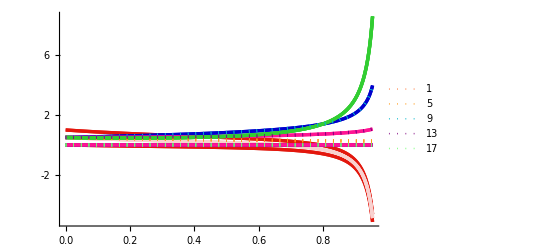
{-Graphics-,-Graphics-}

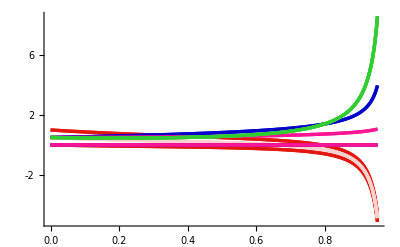
{-Graphics-,-Graphics-}

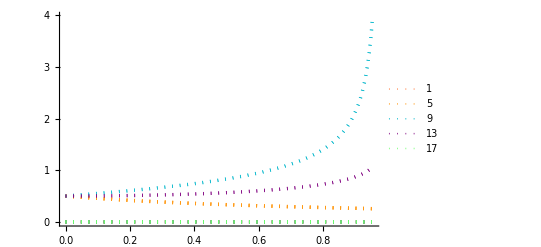
{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

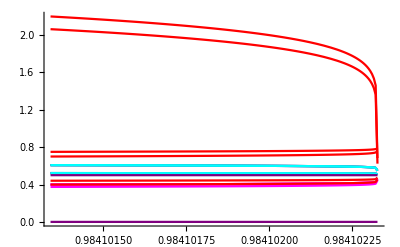
{-Graphics-,-Graphics-}

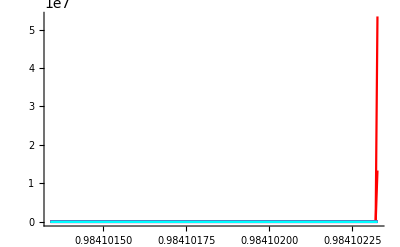
{-Graphics-,-Graphics-}

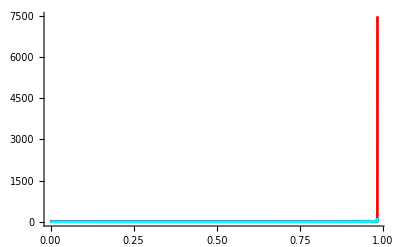
{-Graphics-,-Graphics-}

{{gIV1c0[t]},{gIV1c0[t]}}

{0,0}

{{χDO0[t],χDI0[t]},{χDO0[t],χDI0[t]}}

```mathematica
(* Plotting and analysis *)

gPlotsL0=List[];
gPlotsL1=List[];
vxPlots=List[];
χPlots=List[];
ExpPlots=List[];
gMaxList=ConstantArray[0,q];
vxMaxList=ConstantArray[0,q];
χMaxList=ConstantArray[0,q];
For[band=1,band≤ q,band++,

AppendTo[gPlotsL0,Plot[Evaluate[Evaluate[Re[gList[[1;;5q^2]]/.sols[[band]]]]],{t,0.*domains[[band]],0.97domains[[band]]},PlotRange->All,PlotStyle->Join[ConstantArray[Directive[ColorData["Legacy"]["DeepCadmiumRed"],Thickness[0.006]],q^2] ,ConstantArray[Directive[Lighter[ColorData["Legacy"]["DeepCadmiumRed"],0.8],Thickness[0.006]],q^2] ,ConstantArray[Directive[ColorData["Legacy"]["MediumBlue"],Thickness[0.006]],q^2] ,ConstantArray[Directive[ColorData["Legacy"]["DeepPink"],Thickness[0.006]],q^2] ,ConstantArray[Directive[ColorData["Legacy"]["LimeGreen"],Thickness[0.006]],q^2] ,{Black,Black}],Ticks-> LinTicks, AxesStyle-> Directive[FontSize-> 30,Thickness[0.0015]]]];
AppendTo[gPlotsL1,Plot[Evaluate[Evaluate[Re[gList[[5q^2+1;;10q^2]]/.sols[[band]]]]],{t,0.*domains[[band]],0.97domains[[band]]},PlotRange->All,PlotStyle->Join[ConstantArray[Directive[ColorData["Legacy"]["Oak"],Thickness[0.006],Dotted],q^2] ,ConstantArray[Directive[Lighter[ColorData["Legacy"]["CadmiumYellow"],0.],Thickness[0.006],Dotted],q^2] ,ConstantArray[Directive[ColorData["Legacy"]["Cerulean"],Thickness[0.006],Dotted],q^2] ,ConstantArray[Directive[ColorData["Legacy"]["Purple"],Thickness[0.006],Dotted],q^2] ,ConstantArray[Directive[ColorData["Legacy"]["LightViridian"],Thickness[0.006],Dotted],q^2] ,{Black,Black}], Ticks-> LinTicks,AxesStyle-> Directive[FontSize-> 30,Thickness[0.0015]],PlotLegends->Automatic]];
AppendTo[ExpPlots,Plot[{Evaluate[Abs[Evaluate[1/2+1/2(Log[Abs[χvxList/.sols[[band]]]]/Log[1/(domains[[band]]-t)])/.sols[[band]]]]],0,1/2},{t,0.999999*domains[[band]],domains[[band]]},PlotRange->All,PlotStyle->Join[ConstantArray[Red,q] ,ConstantArray[Magenta,q] ,
ConstantArray[Red,q] ,ConstantArray[Magenta,q] ,
ConstantArray[Red,q] ,ConstantArray[Magenta,q] ,
ConstantArray[Red,q] ,ConstantArray[Magenta,q] ,
ConstantArray[Purple,q] ,ConstantArray[Cyan,q] ,
ConstantArray[Purple,q] ,ConstantArray[Cyan,q] ,
ConstantArray[Purple,q] ,ConstantArray[Cyan,q] ,
ConstantArray[Purple,q] ,ConstantArray[Cyan,q] ,
ConstantArray[Blue,q^2] ,ConstantArray[Green,q^2] ,{Black,Black} ]]];
AppendTo[χPlots,Plot[Evaluate[Abs[χvxList/.sols[[band]]]],{t,0.999999domains[[band]],domains[[band]]},PlotRange->All,PlotStyle->Join[ConstantArray[Red,q] ,ConstantArray[Magenta,q] ,
ConstantArray[Red,q] ,ConstantArray[Magenta,q] ,
ConstantArray[Red,q] ,ConstantArray[Magenta,q] ,
ConstantArray[Red,q] ,ConstantArray[Magenta,q] ,
ConstantArray[Purple,q] ,ConstantArray[Cyan,q] ,
ConstantArray[Purple,q] ,ConstantArray[Cyan,q] ,
ConstantArray[Purple,q] ,ConstantArray[Cyan,q] ,
ConstantArray[Purple,q] ,ConstantArray[Cyan,q] ,ConstantArray[Blue,q^2] ,ConstantArray[Green,q^2] ,{Black,Black} ]]];
AppendTo[vxPlots,Plot[Evaluate[Abs[vxList/.sols[[band]]]],{t,0.domains[[band]],0.99999domains[[band]]},PlotRange->All,PlotStyle->Join[ConstantArray[Red,q] ,ConstantArray[Magenta,q] ,
ConstantArray[Red,q] ,ConstantArray[Magenta,q] ,
ConstantArray[Red,q] ,ConstantArray[Magenta,q] ,
ConstantArray[Red,q] ,ConstantArray[Magenta,q] ,
ConstantArray[Purple,q] ,ConstantArray[Cyan,q] ,
ConstantArray[Purple,q] ,ConstantArray[Cyan,q] ,
ConstantArray[Purple,q] ,ConstantArray[Cyan,q] ,
ConstantArray[Purple,q] ,ConstantArray[Cyan,q] ,ConstantArray[Blue,q^2] ,ConstantArray[Green,q^2] ,{Black,Black} ]]];
gAbsList=Flatten[Abs[gList/.sols[[band]]]/.{t->0.9999domains[[band]]}];
gMaxList[[band]]=gList[[Flatten[Position[gAbsList,Max[gAbsList]]]]];
(*χAbsList=Flatten[Evaluate[SetPrecision[Abs[χvxList/.sols[[band]]]/.{t->0.99999999999999domains[[band]]},1]]];*)
χAbsList=Map[ExponentOnly,Flatten[Evaluate[Abs[χvxList/.sols[[band]]]/.{t->0.9999999999domains[[band]]}]]];
χMaxList[[band]]=χvxList[[Flatten[Position[χAbsList,Max[χAbsList]]]]];
]
Table[Show[gPlotsL0[[j]],gPlotsL1[[j]]],{j,1,Length[ExpPlots]}]
Table[Show[gPlotsL0[[j]]],{j,1,Length[ExpPlots]}]
Table[Show[gPlotsL1[[j]]],{j,1,Length[ExpPlots]}]
Table[Show[gPlotsL1[[j]]],{j,1,Length[ExpPlots]}]
Table[Show[ExpPlots[[j]]],{j,1,Length[ExpPlots]}]
Table[Show[χPlots[[j]]],{j,1,Length[vxPlots]}]
Table[Show[vxPlots[[j]]],{j,1,Length[vxPlots]}]
gMaxList
vxMaxList
χMaxList
```

```mathematica
SetOptions[LinTicks,MajorTickLength->{0.02,0},MinorTickLength->{0.013,0},MajorTickStyle-> Thickness[0.003],MinorTickStyle-> Thickness[0.003]];
```

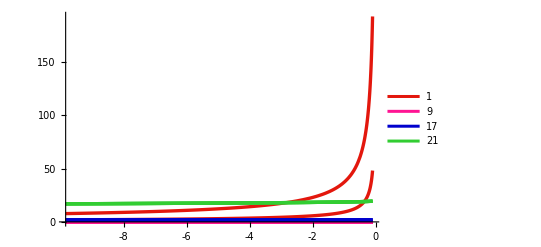

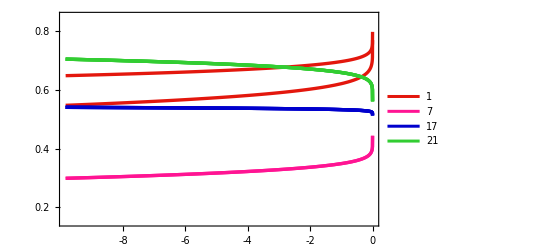

```mathematica
Plot[Evaluate[Abs[χvxList/.sols[[1]]]/.{t->domains[[1]]+u 10^(-4)}],{u,(0.999-1)domains[[1]]*10^4,(0.99999-1)domains[[1]]10^4},PlotRange->All,PlotStyle->Join[ConstantArray[Directive[ColorData["Legacy"]["DeepCadmiumRed"],Thickness[0.006]],4q] ,ConstantArray[Directive[ColorData["Legacy"]["DeepPink"],Thickness[0.006]],4q] ,ConstantArray[Directive[ColorData["Legacy"]["MediumBlue"],Thickness[0.006]],q^2] ,ConstantArray[Directive[ColorData["Legacy"]["LimeGreen"],Thickness[0.006]],q^2] ,{Black,Black} ],AxesStyle-> Directive[FontSize-> 30,Thickness[0.0015]],PlotLegends->Automatic,AxesOrigin->{(0.999-1)domains[[1]]10^4,0},Ticks-> LinTicks]

Plot[Evaluate[Flatten[Evaluate[1/2+1/2(Log[Abs[χvxList/.sols[[1]]]]/Log[1/(domains[[1]]-t)])/.{t->domains[[1]]+u 10^(-4)}]]],{u,(0.999-1)domains[[1]]*10^4,(1-1)domains[[1]]10^4},PlotRange->{All,{0.15,0.85}},PlotStyle->Join[ConstantArray[Directive[ColorData["Legacy"]["DeepCadmiumRed"],Thickness[0.006]],q] ,ConstantArray[Directive[Transparent,Thickness[0.006]],4] ,ConstantArray[Directive[ColorData["Legacy"]["DeepPink"],Thickness[0.006]],q] ,ConstantArray[Directive[Transparent,Thickness[0.006]],4q],ConstantArray[Directive[ColorData["Legacy"]["MediumBlue"],Thickness[0.006]],q^2] ,ConstantArray[Directive[ColorData["Legacy"]["LimeGreen"],Thickness[0.006]],q^2] ,{Black,Black} ],AxesStyle-> Directive[FontSize-> 30,Thickness[0.0015]],PlotLegends->Automatic,AxesOrigin->{(1-1)domains[[1]]10^4,0.5},Frame-> True,PlotRangePadding->0.02,FrameStyle-> Directive[FontSize-> 40,Thickness[0.0015]],FrameTicks->{{LinTicks,None},{LinTicks,None}},PlotRangePadding-> None]
```